Both of the following examples are taken from Neubert and Caswell 1997, 
“Alternatives to Resilience for Measuring the Responses of Ecological Systems to Perturbations”

```mathematica
(* set directory for image exports *)
SetDirectory[ParentDirectory[NotebookDirectory[]]]
```

/Users/gracezhang/Documents/GitHub/Oral_Exam_Paper

Positive Reactivity example with real eigenvalues.

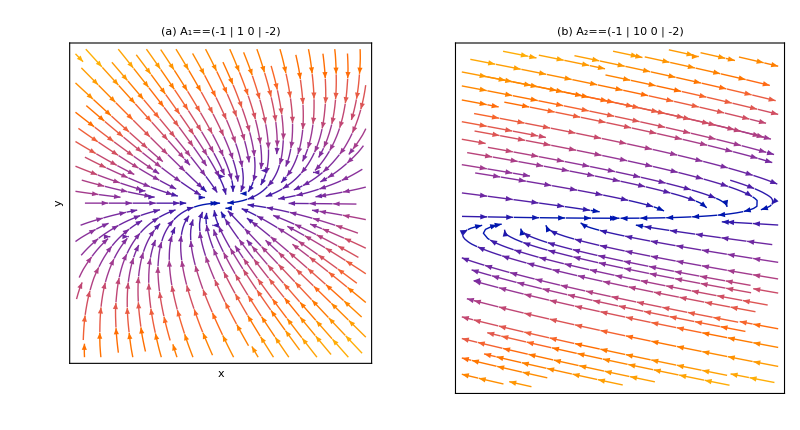

figs/positive_reactivity_real_example.jpeg

```mathematica
plot1 = Show[StreamPlot[{-x+y,-2y},{x,-1,1},{y,-1,1},AxesLabel->{x,y} ,PlotLabel-> "(a)     "Text[Subscript[A, 1] == {{-1,1},{0,-2}}], FrameTicks->None]];
plot2 = Show[StreamPlot[{-x+10y,-2y},{x,-1,1},{y,-1,1},PlotLabel->"(b)     "Text[Subscript[A, 2] == {{-1,10},{0,-2}}] , FrameTicks->None]];
real= GraphicsRow[{plot1, plot2}]
Export["figs/positive_reactivity_real_example.jpeg", real]
```

```mathematica
Eigenvectors[{{-1,1},{0,-2}}]
Eigenvectors[{{-1,10},{0,-2}}]
```

{{-1,1},{1,0}}

{{-10,1},{1,0}}

## Positive Reactivity example with complex eigenvalues.

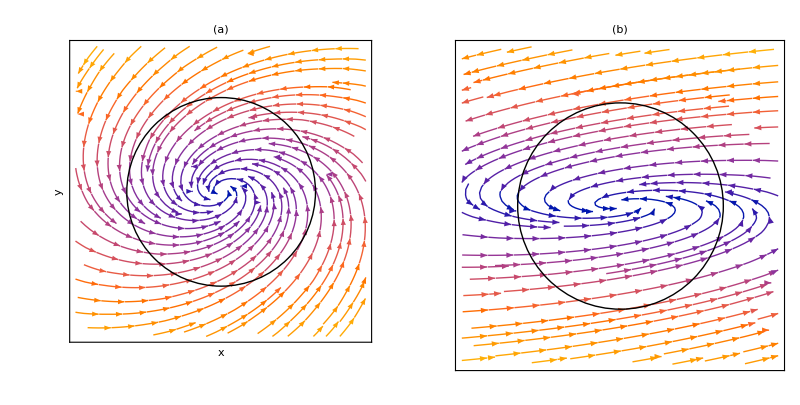

figs/positive_reactivity_complex_example.jpeg

```mathematica
plot1 = Show[StreamPlot[{-x-4y,2.25x-2y},{x,-1,1},{y,-1,1},AxesLabel->{x,y} ,PlotLabel->"(a)", FrameTicks->None], Graphics[Circle[{0,0},0.65]]];
plot2 = Show[StreamPlot[{-x-12y,0.75x-2y},{x,-1,1},{y,-1,1},PlotLabel->"(b)" , FrameTicks->None], Graphics[Circle[{0,0},0.65]]];
complex= GraphicsRow[{plot1, plot2}]
Export["figs/positive_reactivity_complex_example.jpeg", complex]
```